```mathematica
<<MaTeX`
```

```mathematica
DSolve[{y'[x]==Log[2]/N y[x],y[0]==A},y[x],x]
```

{{y[x]→2^(x/N) A}}

```mathematica
DSolve[{y'[x]==λ y[x],y[0]==A},y[x],x]//Flatten
Integrate[y[x]/.%,{x,0,∞}]
```

{y[x]→A ⅇ^(x λ)}

ConditionalExpression[-A/λ,Re[λ]<0]

```mathematica
RSolve[{(y[n+1]-y[n])/1==λ y[n],y[0]==A},y[n],n]//Flatten
∑_(n=0)^∞ y[n]/.%
```

{y[n]→A (1+λ)^n}

-A/λ

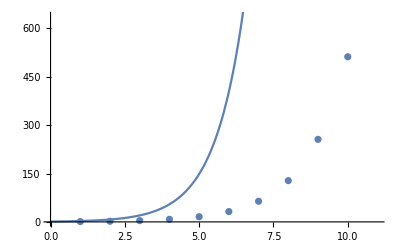

```mathematica
With[{λ=1},
Show[ListPlot[Table[(1+λ)^n,{n,0,10}]],Plot[ⅇ^(x λ),{x,0,10}]]
]
```

```mathematica
Solve[2==ⅇ^(α t),t]
```

{{t→ConditionalExpression[(2 ⅈ π C[1]+Log[2])/α,C[1]∈Integers]}}

```mathematica
Log[2]/0.03
```

23.1049

```mathematica
DSolve[y'[t]==λ[t]y[t],y[t],t]//Flatten
Block[{λ},
λ[t_]=Exp[-t];
y[t]/.%/.C[1]->1
]
```

{y[t]→ⅇ^(∫_1^t λ[K[1]]ⅆK[1]) C[1]}

ⅇ^(1/ⅇ-Cosh[t]+Sinh[t])

```mathematica
Limit[ⅇ^(1/ⅇ-Cosh[t]+Sinh[t]),t->∞]
%//N
```

ⅇ^(1/ⅇ)

1.44467

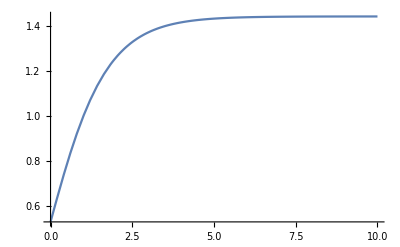

```mathematica
Plot[ⅇ^(1/ⅇ-Cosh[t]+Sinh[t]),{t,0,10},PlotRange->All]
```

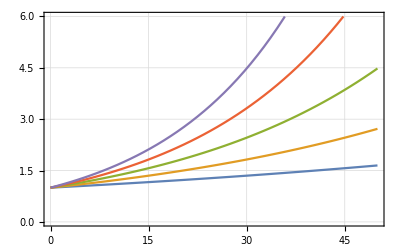

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->10};
Plot[Evaluate@Table[ⅇ^(λ t),{λ,0.01,0.05,0.01}],{t,0,50},PlotLegends->Placed[MaTeX[{"\\lambda=0.01","\\lambda=0.02","\\lambda=0.03","\\lambda=0.04","\\lambda=0.05"},FontSize->10],Right],PlotTheme->"Detailed",FrameLabel->MaTeX[{"t","y(t)"},FontSize->10],PlotLabel->MaTeX["y(t)=e^{\\lambda t}",FontSize->10],PlotRange->{All,{0,6}},BaseStyle->texStyle]
(*Export["~/Desktop/exp.png",%,ImageResolution->200,ImageSize->1000]*)
```

```mathematica
?PlotTheme
```

PlotTheme is an option for plotting and related functions that specifies an overall theme for visualization elements and styles.